## NaCs 1Σ Hamiltonian, excluding hyperfine terms, including dipole-dipole interactions

## Description

This code simulates the dipolar interaction between two adjacent molecules. The full Hamiltonian of the molecules includes hyperfine states, which I ignore here. This assumption I am making is that if we initially populate a particular hyperfine state in N=0 with STIRAP (in our case, |I_Na=3/2, mI_Na=3/2, I_Cs=7/2, mI_Cs=5/2⟩ ), then we keep the same quantum numbers as we go to states with higher rotational quantum number N. This approximation is pretty good. At our large B-field of 860 G and large trap depth of several MHz, the nuclear spins and rotational angular momentum are almost fully uncoupled; the nuclear spins will point along the B field, and the rotational angular momentum will point along the tweezer AC electric field.

## Setup

### Helper functions

```mathematica
kp[a_,b_]:=KroneckerProduct[a,b](*shorthand Kronecker product*)
conj=Complex[a_,b_]->Complex[a,-b];(*shorthand complex conjugate*)
{αpar,αperp,α0,Δ,B,U,Int,d,r,ϵ0,h}=.;
```

### Constants

Constants of NaCs. Polarizability defined for 1064 nm.

```mathematica
αpar=1872.12;
αperp=467.038;
Δ=αpar-αperp;
α0=(αpar+2αperp)/3;
B=1.7396 10^9;
d=Quantity[4.6,"Debyes"]//UnitConvert//QuantityMagnitude;
ϵ0=Quantity["Permittivity of free space"]//UnitConvert//QuantityMagnitude;
h=Quantity["PlanckConstant"]//UnitConvert//QuantityMagnitude;
r=Quantity[2.6,"Micrometers"]//UnitConvert//QuantityMagnitude;
constantValues={αpar,αperp,α0,Δ,B,d,ϵ0,h,r};
{αpar,αperp,α0,Δ,B,d,ϵ0,h,r}=.;
constantLabels={αpar,αperp,α0,Δ,B,d,ϵ0,h,r};
constants=Normal[AssociationThread[constantLabels->constantValues//N]];
```

### Hilbert space

Defines the single particle and multi-particle Hilbert spaces. For each state in the Hilbert space, there is an associated label with its quantum numbers.

#### Single particle

```mathematica
nM=2; (*maximum rotational angular momentum N*)
nℋ1=Sum[2j+1,{j,0,nM}]; (*number of states in the Hilbert space*)
nP=2;(*number of particles that interact*)

ℋ1=IdentityMatrix[nℋ1];(*single particle Hilbert space*)
sℋ1=Partition[ℋ1,{nℋ1,1}][[1]];(*states in the single particle Hilbert space*)
lℋ1=Flatten[Table[{n,m},{n,0,nM},{m,-n,n}],1];(*state labels |N,m⟩*)
yℋ1=Flatten[Table[SphericalHarmonicY[n,m,θ,ϕ],{n,0,nM},{m,-n,n}],1];(*Spherical harmonics Subscript[Y, n,m]*)
s2lℋ1=AssociationThread[sℋ1->lℋ1];
l2sℋ1=AssociationThread[lℋ1->sℋ1]; 
l2yℋ1=AssociationThread[lℋ1->yℋ1]; 
y2lℋ1=AssociationThread[yℋ1->lℋ1];
```

#### Multi-particle

```mathematica
ℋn=IdentityMatrix[nℋ1^nP];(*multi-particle Hilbert space*)
nℋn=Length[ℋn];(*number of states in the multi-particle Hilbert space*)
sℋn=Partition[ℋn,{nℋ1^nP,1}][[1]];(*states in the multi-particle Hilbert space*)
lℋn=Flatten[Table[{{ni,mi},{nj,mj}},{ni,0,nM},{mi,-ni,ni},{nj,0,nM},{mj,-nj,nj}],3];(*multi-particle state labels |Subscript[N, i],Subscript[m, i]⟩|Subscript[N, j],Subscript[m, j]⟩*)
s2lℋn=AssociationThread[sℋn->lℋn];
l2sℋn=AssociationThread[lℋn->sℋn];
```

### Polarization ellipse

Defines the tweezer polarization seen by the molecule, and calculates the angle between the quantization axis and the array.

```mathematica
{θ,ϕ,θd}=.;
qwp[θ_]=Exp[-(ⅈ π)/4]({{Cos[θ]^2+ⅈ Sin[θ]^2, (1-ⅈ) Sin[θ]Cos[θ]}, {(1-ⅈ) Sin[θ]Cos[θ], Sin[θ]^2+ⅈ Cos[θ]^2}});(*quarter waveplate Jones matrix*)
hwp[θ_]=Exp[-(ⅈ π)/2]({{Cos[θ]^2-Sin[θ]^2, 2Cos[θ]Sin[θ]}, {2Cos[θ]Sin[θ], Sin[θ]^2-Cos[θ]^2}});(*half waveplate Jones matrix*)
lpr[η_,θ_]=Exp[-(ⅈ η)/2]({{Cos[θ]^2+Exp[ⅈ η] Sin[θ]^2, (1-Exp[ⅈ η])Cos[θ]Sin[θ]}, {(1-Exp[ⅈ η])Cos[θ]Sin[θ], Sin[θ]^2+Exp[ⅈ η] Cos[θ]^2}});(*linear phase retarder Jones matrix*)

jH=({{1}, {0}});jV=({{0}, {1}});jL=1/(√2)({{1}, {ⅈ}});jR=1/(√2)({{1}, {-ⅈ}});(*Jones vectors for horizontal, vertical, LCP, and RCP light*)
jF[θh_,θq_]=FullSimplify[Flatten[hwp[θh].qwp[θq].jH],Assumptions->{0<=θh<2π,0<=θq<2π}];(*Jones vector seen by molecules*)

pEllipse[θh_,θq_]=FullSimplify[ComplexExpand[Re[jF[θh,θq]Exp[-ⅈ t]]],Assumptions->{t>0,0<=θh<2π,0<=θq<2π}];(*Visualization of the polarization ellipse*)
θd[θh_,θq_]:=ArcCos[Sin[2θh-θq]](*Angle between minor axis and array*)
```

### Polarizability

Defines the Hamiltonian for light shifts produced by the AC electric field.

```mathematica
{ϵ,n1,m1,n2,m2}=.;
α=({{αperp, 0, 0}, {0, αperp, 0}, {0, 0, αpar}});(*Polarizability tensor in the molecular frame. It is diagonal for a linear molecule*)
Rx=RotationMatrix[θ,{1,0,0}];
Ry=RotationMatrix[θ,{0,1,0}];
Rz=RotationMatrix[ϕ,{0,0,1}];
ϵ[θh_,θq_]={Append[jF[θh,θq],0]}ᵀ;(*Jones vector seen by the molecule, expressed in 3D coordinates*)
β[θ_,ϕ_]=-U/α0((ϵ[θh,θq]ᵀ/.Complex[a_,b_]->Complex[a,-b]).Rzᵀ.Ryᵀ.α.Ry.Rz.ϵ[θh,θq]-(αpar+2αperp)/3//FullSimplify)[[1,1]]/.(αpar-αperp)->Δ;(*Differential light shift relative to N=0. The rotation matrices express the polarizability tensor in the lab frame.*)
srAC[{n1_,m1_},{n2_,m2_}]:=(n1==n2∨Abs[n1-n2]==2)∧(m1==m2∨Abs[m1-m2]==2)(*Selection rules for coupling between states*)
```

### Dipole-dipole interaction

```mathematica
dpME[q_,{Nb_,mb_},{Nk_,mk_}]:=Quiet[(-1)^mb √((2 Nb+1) (2 Nk+1)) ThreeJSymbol[{Nb,-mb},{1,q},{Nk,mk}] ThreeJSymbol[{Nb,0},{1,0},{Nk,0}]](*dipole matrix element for spherical component q between bra Nm and ket Nm*)
HddME[{b1_,b2_},{k1_,k2_}]:=dpME[0,b1,k1]dpME[0,b2,k2]+(dpME[1,b1,k1]dpME[-1,b2,k2]+dpME[-1,b1,k1]dpME[1,b2,k2])/2
srDD[{{bn1_,bm1_},{bn2_,bm2_}},{{kn1_,km1_},{kn2_,km2_}}]:={bn1,bm1}=={kn2,km2}∧{bn2,bm2}=={kn1,km1}∧Abs[bn1-bn2]==1
```

### Hamiltonians

#### Single particle

```mathematica
H0ℋ1=SparseArray[{i_,i_}->2B lℋ1[[i,1]],{nℋ1,nℋ1}]//Quiet;(*Rotation Hamiltonian*)
Hacℋ1=SparseArray[ParallelTable[If[srAC[lℋ1[[i]],lℋ1[[j]]],Integrate[(yℋ1[[i]]/.conj)yℋ1[[j]]β[θ,ϕ]Sin[θ],{θ,0,π},{ϕ,0,2π},Assumptions->{θh>0,θq>0,Δ>0},GenerateConditions->True],0],{i,1,nℋ1},{j,1,nℋ1}]];(*Off-resonant AC-electric field Hamiltonian*)
Ω={Ωm,Ω0,Ωp};
HΩℋ1=Sum[Ω[[q+2]]l2sℋ1[{0,0}].l2sℋ1[{1,q}]ᵀ,{q,-1,1}]+Sum[Ω[[q+2]]l2sℋ1[{0,0}].l2sℋ1[{1,q}]ᵀ,{q,-1,1}]ᵀ+Sum[-ΔΩ l2sℋ1[{1,q}].l2sℋ1[{1,q}]ᵀ,{q,-1,1}];
Hℋ1=H0ℋ1+Hacℋ1+HΩℋ1;
```

```mathematica
mat=Normal[Hacℋ1+H0ℋ1]/.constants/.{θh->0,θq->π/2-ArcCos[1/(√3)]+Δθ,U->10^6};
```

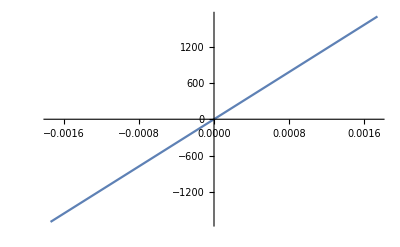

```mathematica
Plot[Select[Re[Eigenvalues[mat]-4B/.constants],-1 10^4<#<10^4&]-Select[Re[Eigenvalues[mat]-2B/.constants],-1 10^4<#<10^4&],{Δθ,(-.1π)/180,(.1 π)/180}]
```

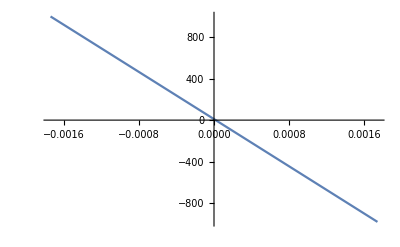

```mathematica
Plot[Select[Re[Eigenvalues[mat]-2B/.constants],-1 10^4<#<10^4&]-Select[Re[Eigenvalues[mat]-0B/.constants],-1 10^4<#<10^4&],{Δθ,(-.1π)/180,(.1 π)/180}]
```

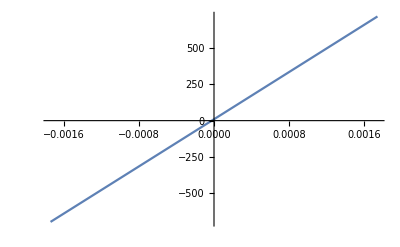

```mathematica
Plot[Select[Re[Eigenvalues[mat]-4B/.constants],-1 10^4<#<10^4&]-Select[Re[Eigenvalues[mat]-0B/.constants],-1 10^4<#<10^4&],{Δθ,(-.1π)/180,(.1 π)/180}]
```

```mathematica
eigs[[1]]/.θq->0//N
```

{-0.0952381,0.133333,-0.0952381,0.133333,-0.266667,0.190476,-0.408222,0.190476,0.217746}

#### Multi-particle

```mathematica
H1ℋn=kp[Hℋ1,ℋ1]+kp[ℋ1,Hℋ1];
Hddℋn=d^2(1-3 Cos[Hold[θd[θh,θq]]]^2)/(4π ϵ0 h r^3)SparseArray[{i_,j_}/;srDD[lℋn[[i]],lℋn[[j]]]->HddME[lℋn[[i]],lℋn[[j]]],{nℋn,nℋn}]//Quiet;
Hℋn=H1ℋn+Hddℋn;
```

#### Show Hamiltonians

```mathematica
(#//MatrixForm)&/@{H0ℋ1,Hacℋ1,HΩℋ1};
Hddℋn/(d^2(1-3 Cos[Hold[θd[θh,θq]]]^2)/(4π ϵ0 h r^3))//MatrixForm;
```

#### Eigenvalues

```mathematica
{evalsAC,evecsAC}=Eigensystem[Hacℋ1]//FullSimplify;
```

## Results

### Choose polarization ellipse

```mathematica
{angles,evecsACn,noPulse,Hn}=.;
```

```mathematica
angles={θh->π/2-ArcCos[1/(√3)]/2,θq->π/2-ArcCos[1/(√3)]};
(*angles={θh->0,θq->π/2-ArcCos[1/(√3)]};*)
Manipulate[ParametricPlot[pEllipse[θh,θq]/.angles,{t,0,2π},ImageSize->Small,AxesLabel->{"x","y"},PlotLabel->StringForm["θ_d=°",Round[180/π θd[θh,θq]//Quiet,0.1]]],{{θh,θh/.angles},0,2π},{{θq,θq/.angles},0,2π}](*view the polarization ellipse*)
```

ReplaceAll::reps: {angles} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

ReplaceAll::reps: {angles} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

ReplaceAll::reps: {angles} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

ReplaceAll::reps: {angles} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

ReplaceAll::reps: {angles} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

### Find AC eigenstates

```mathematica
evecsACn={(Normalize/@(evecsAC/.angles/.constants//N//Chop))[[#]]}ᵀ&/@{1,2,3,4};
```

### Dipolar interaction

Interaction from 0_i 1_jto 1_i 0_j, where i and j are sites and 0 and 1 represent N=0 and N=1 states:

```mathematica
noPulse={Ωm->0,Ω0->0,Ωp->0,ΔΩ->0};
Hn=ReleaseHold[Hℋn/.r->1.5 10^-6/.noPulse/.angles/.constants/.U->10^6];
```

```mathematica
SetOptions[Plot,BaseStyle->{FontFamily->"Arial",FontSize->20},TicksStyle->Directive[Black,10],Frame->True,FrameTicks->{Automatic,Automatic},ImagePadding->{{80,10},{80,10}},ImageSize->500,AxesLabel->{"",""},PlotStyle->Black]; 
p2=Plot[Evaluate@(Abs[kp[sℋ1[[1]],evecsACn[[#]]]ᵀ.Quiet[MatrixExp[-ⅈ 2π t 10^-3 Hn]].kp[evecsACn[[#]],sℋ1[[1]]]]^2&/@{3}),{t,0,5 },FrameLabel->{"t (ms)","Magic state pop. on site 2"},PlotStyle->ColorData[3,4],PlotLegends->{"r=1.6"}]
```

Plot::nonopt: Options expected (instead of PlotLegends) beyond position 2 in Plot[{{{Abs[0.+Times[«2»]+Times[«2»]]^2}}},{t,0,5},FrameLabel→{t (ms),Magic state pop. on site 2},PlotStyle→ColorData[3,4],PlotLegends]. An option must be a rule or a list of rules.

Plot[{{{(Abs[0.+0.707107 (0.+0.707107 ((4.65644×10^-6+0.5 ⅈ) ((0.+0. ⅈ)-(4.65644×10^-6-0.5 ⅈ) (1. Cos[2.18592×10^7 t]-(0.+1. ⅈ) Sin[2.18592×10^7 t]))+(0.0894336+0.491937 ⅈ) ((0.+0. ⅈ)+(0.0894336-0.491937 ⅈ) (ⅇ^(9.31323×10^-10 t) Cos[2.18592×10^7 t]-ⅈ ⅇ^(9.31323×10^-10 t) Sin[2.18592×10^7 t]))+(0.209548+0.453971 ⅈ) ((0.+0. ⅈ)-(0.209548-0.453971 ⅈ) (ⅇ^(2.79403×10^-9 t) Cos[2.18605×10^7 t]-ⅈ ⅇ^(2.79403×10^-9 t) Sin[2.18605×10^7 t]))-(0.0000120584-0.5 ⅈ) ((0.+0. ⅈ)-(0.0000120584+0.5 ⅈ) (ⅇ^(-1.77427×10^-17 t) Cos[2.18605×10^7 t]-ⅈ ⅇ^(-1.77427×10^-17 t) Sin[2.18605×10^7 t])))-0.707107 ((4.65644×10^-6+0.5 ⅈ) ((0.+0. ⅈ)-(4.65644×10^-6-0.5 ⅈ) (1. Cos[2.18592×10^7 t]-(0.+1. ⅈ) Sin[2.18592×10^7 t]))+(0.0894336+0.491937 ⅈ) ((0.+0. ⅈ)+(0.0894336-0.491937 ⅈ) (ⅇ^(9.31323×10^-10 t) Cos[2.18592×10^7 t]-ⅈ ⅇ^(9.31323×10^-10 t) Sin[2.18592×10^7 t]))-(0.209548+0.453971 ⅈ) ((0.+0. ⅈ)-(0.209548-0.453971 ⅈ) (ⅇ^(2.79403×10^-9 t) Cos[2.18605×10^7 t]-ⅈ ⅇ^(2.79403×10^-9 t) Sin[2.18605×10^7 t]))+(0.0000120584-0.5 ⅈ) ((0.+0. ⅈ)-(0.0000120584+0.5 ⅈ) (ⅇ^(-1.77427×10^-17 t) Cos[2.18605×10^7 t]-ⅈ ⅇ^(-1.77427×10^-17 t) Sin[2.18605×10^7 t]))))-0.707107 (0.+0.707107 ((4.65644×10^-6+0.5 ⅈ) ((0.+0. ⅈ)-(4.65644×10^-6-0.5 ⅈ) (1. Cos[2.18592×10^7 t]-(0.+1. ⅈ) Sin[2.18592×10^7 t]))+(0.0894336+0.491937 ⅈ) ((0.+0. ⅈ)+(0.0894336-0.491937 ⅈ) (ⅇ^(9.31323×10^-10 t) Cos[2.18592×10^7 t]-ⅈ ⅇ^(9.31323×10^-10 t) Sin[2.18592×10^7 t]))+(0.209548+0.453971 ⅈ) ((0.+0. ⅈ)+(0.209548-0.453971 ⅈ) (ⅇ^(2.79403×10^-9 t) Cos[2.18605×10^7 t]-ⅈ ⅇ^(2.79403×10^-9 t) Sin[2.18605×10^7 t]))-(0.0000120584-0.5 ⅈ) ((0.+0. ⅈ)+(0.0000120584+0.5 ⅈ) (ⅇ^(-1.77427×10^-17 t) Cos[2.18605×10^7 t]-ⅈ ⅇ^(-1.77427×10^-17 t) Sin[2.18605×10^7 t])))-0.707107 ((4.65644×10^-6+0.5 ⅈ) ((0.+0. ⅈ)-(4.65644×10^-6-0.5 ⅈ) (1. Cos[2.18592×10^7 t]-(0.+1. ⅈ) Sin[2.18592×10^7 t]))+(0.0894336+0.491937 ⅈ) ((0.+0. ⅈ)+(0.0894336-0.491937 ⅈ) (ⅇ^(9.31323×10^-10 t) Cos[2.18592×10^7 t]-ⅈ ⅇ^(9.31323×10^-10 t) Sin[2.18592×10^7 t]))-(0.209548+0.453971 ⅈ) ((0.+0. ⅈ)+(0.209548-0.453971 ⅈ) (ⅇ^(2.79403×10^-9 t) Cos[2.18605×10^7 t]-ⅈ ⅇ^(2.79403×10^-9 t) Sin[2.18605×10^7 t]))+(0.0000120584-0.5 ⅈ) ((0.+0. ⅈ)+(0.0000120584+0.5 ⅈ) (ⅇ^(-1.77427×10^-17 t) Cos[2.18605×10^7 t]-ⅈ ⅇ^(-1.77427×10^-17 t) Sin[2.18605×10^7 t]))))])^2}}},{t,0,5},FrameLabel→{t (ms),Magic state pop. on site 2},PlotStyle→ColorData[3,4],PlotLegends]

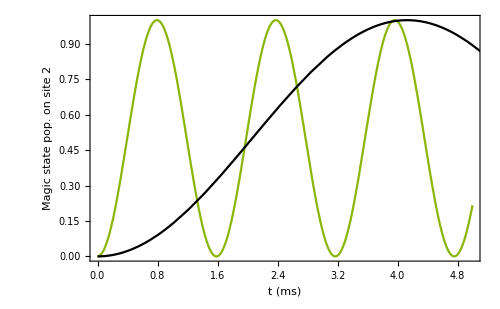

```mathematica
Show[p2,p1]
```

```mathematica
1.2/550
```

0.00218182

```mathematica
r/.constants
```

2.6×10^-6

```mathematica
yℋn=lℋn/.Association[Table[{n,mN}->SphericalHarmonicY[n,mN,θ,ϕ],{n,0,1},{mN,-n,n}]];
```

```mathematica
r=0.4;TableForm[{SphericalPlot3D[Abs[Flatten[MatrixExp[-ⅈ 2π # 10^-3 Hn].kp[evecsACn[[4]],sℋ1[[1]]]].yℋn[[All,1]]]^2,{θ,0,π},{ϕ,0,2π},PlotRange->{{-r,r},{-r,r},{-r,r}},ViewPoint->Above],SphericalPlot3D[Abs[Flatten[MatrixExp[-ⅈ 2π # 10^-3 Hn].kp[evecsACn[[4]],sℋ1[[1]]]].yℋn[[All,2]]]^2,{θ,0,π},{ϕ,0,2π},PlotRange->{{-r,r},{-r,r},{-r,r}},ViewPoint->Above]}&/@Range[0,16,4]]
```

```mathematica
ψ=MatrixExp[-ⅈ 2π 0 10^-3 Hn].kp[evecsACn[[4]],sℋ1[[1]]];
ρAB=ψ.ψ†;
ρA=Sum[kp[ℋ1,sℋ1[[j]]ᵀ].ρAB.kp[ℋ1,sℋ1[[j]]],{j,1,nℋ1}];
ρB=Sum[kp[sℋ1[[j]]ᵀ,ℋ1].ρAB.kp[sℋ1[[j]],ℋ1],{j,1,nℋ1}];
eA=Eigensystem[ρA];
eA=Sort[eAᵀ]ᵀ;
eB=Eigensystem[ρB];
eB=Sort[eBᵀ]ᵀ;

(*SphericalPlot3D[Abs[Flatten[Sum[#.sℋ1[[i]],{i,1,nℋ1}]].yℋ1]^2,{θ,0,π},{ϕ,0,2π}]&/@{ρA,ρB}*)
```

```mathematica
r=0.3;Table[SphericalPlot3D[(Abs[eA[[2]].yℋ1]^2)[[i]]eA[[1,i]],{θ,0,π},{ϕ,0,2π},PlotRange->{{-r,r},{-r,r},{-r,r}}],{i,1,4}]
```

{-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-}

```mathematica
pl[t_]:=Module[{ψ,ρAB,ρA,ρB,eA,eB},ψ=MatrixExp[-ⅈ 2π t 10^-3 Hn].kp[evecsACn[[4]],sℋ1[[1]]];
ρAB=ψ.ψ†;
ρA=Sum[kp[ℋ1,sℋ1[[j]]ᵀ].ρAB.kp[ℋ1,sℋ1[[j]]],{j,1,nℋ1}];
ρB=Sum[kp[sℋ1[[j]]ᵀ,ℋ1].ρAB.kp[sℋ1[[j]],ℋ1],{j,1,nℋ1}];
eA=Eigensystem[ρA];
eA=Sort[eAᵀ]ᵀ;
eB=Eigensystem[ρB];
eB=Sort[eBᵀ]ᵀ;
Table[SphericalPlot3D[(Abs[eA[[2]].yℋ1]^2)[[i]]eA[[1,i]],{θ,0,π},{ϕ,0,2π},PlotRange->{{-r,r},{-r,r},{-r,r}}],{i,1,4}]]
```

```mathematica
Table[{pl[t]},{t,0,10,2}]
```

```mathematica
ψ
```

{{0.+0. ⅈ},{0.+0. ⅈ},{0.+0. ⅈ},{0.+0. ⅈ},{-0.707107+0. ⅈ},{0.+0. ⅈ},{0.+0. ⅈ},{0.+0. ⅈ},{0.+0. ⅈ},{0.+0. ⅈ},{0.+0. ⅈ},{0.+0. ⅈ},{0.707107+0. ⅈ},{0.+0. ⅈ},{0.+0. ⅈ},{0.+0. ⅈ}}

```mathematica
yℋn[[All,1]].ψ
```

{(0.+0. ⅈ)-(0.244301+0. ⅈ) ⅇ^(-ⅈ ϕ) Sin[θ]-(0.244301+0. ⅈ) ⅇ^(ⅈ ϕ) Sin[θ]}

```mathematica
ψ=MatrixExp[-ⅈ 2π 0 10^-3 Hn].kp[evecsACn[[4]],sℋ1[[1]]];
ρAB=ψ.ψ†;
eAB=Eigensystem[ρAB];
eAB=Sort[eABᵀ]ᵀ;
eAB[[2,-1]]
```

{0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,-0.707107+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.707107+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ}

```mathematica
Flatten[ψ]
```

{0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,-0.707107+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.707107+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ}

```mathematica
-1.51673+25.5749 0.095
```

0.912886

```mathematica
1/0.785
```

1.27389